This is a program written to find out what exactly happened when new perturbations of matter profiles are added.

# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

```mathematica
Get["../../neuPackage/neumat.wl"]
```

# New Combinations of n’s

## Parameters

```mathematica
gF=1.17*10^(-11)(*MeV^(-2)*)
ye=0.5
```

1.17×10^-11

0.5

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
energy20=20;(*Energy in units of MeV*)
omegaV=deltamsquare13/(2 energy20)(*MeV*);(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093/2]
```

0.153077

```mathematica
fraction=0.5
lambdaN=fraction*Cos[2thetaV]omegaV
```

0.5

3.09888×10^-17

```mathematica
Cos[2thetaV]-(lambdaN/omegaV)^2
```

0.726209

```mathematica
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
init={psi1[0],psi2[0]}=={1,0};
endpointN=1600;
```

List of Parameters for 1 2 3 frequiencies

```mathematica
onekList={0.999};
twokList={0.999,0.6};
oneaList={0.1};
twoaList={0.1,0.1};
onephiList={0};
twophiList={0,0};
threekList={0.999,0.6,0.4};
threeaList={0.1,0.1,0.1};
threephiList={0,0,0};
thetaVRes=thetaV;
thetamVRes=thetamV;
omegaVRes=omegaV;
endpointNRes=endpointN*15(*/20*)
```

24000

## Superposition

```mathematica
oneListFullTicks=Table[{x,ScientificForm[MeVInverse2km[x/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]],2]},{x,0,endpointNRes}];
```

```mathematica
oneListTicks=Take[oneListFullTicks,{1,Length@oneListFullTicks,Floor[(Length@oneListFullTicks)/5]}];
```

```mathematica
oneListTicks
```

{{0,0.},{4800,2.×10^7},{9600,3.9×10^7},{14400,5.9×10^7},{19200,7.8×10^7},{24000,9.8×10^7}}

```mathematica
oneNPlt=pltNum[onekList,oneaList,onephiList,thetamVRes,endpointNRes,"Single Frequency",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
oneListPlt=pltNList[{{1}},onekList,oneaList,onephiList,thetamVRes,endpointNRes,"Single Frequency",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
twoNPlt=pltNum[twokList,twoaList,twophiList,thetamVRes,endpointNRes,"Two Frequencies",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
twoEffectiveList=Flatten[ Drop[Part[qValueOrderdList[listNGenerator[2,4],twokList,twoaList,twophiList,thetamVRes],1;;2],None,{2}],1]
```

{{1,0},{0,1}}

```mathematica
twoListPlt=pltNList[twoEffectiveList,twokList,twoaList,twophiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
threeNPlt=pltNum[threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Three Frequencies Numerical",{Red,Dashed},oneListTicks,"Distance (km)"];
```

```mathematica
threeEffectiveList=Flatten[ Drop[Part[qValueOrderdList[listNGenerator[3,4],threekList,threeaList,threephiList,thetamVRes],1;;4],None,{2}],1]
```

{{0,-1,4},{0,1,1},{0,3,-2},{1,0,0}}

```mathematica
threeListPlt=pltNList[{threeEffectiveList[[2]],threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"];
```

```mathematica
(*Grid[{{Show[oneListPlt,oneNPlt]},{Show[twoListPlt,twoNPlt]},{Show[threeListPlt,threeNPlt]}}]*)
```

### Can we just linearly add up all the oscillations from each combinations of n’s?

For two frequency case, we have the useful combination to be

```mathematica
twoEffectiveList
```

{{1,0},{0,1}}

Now we grab the each one and make lists of transition probabilities

```mathematica
phi2ListDataNList[listInput_,kNList_,aNList_,phiNList_,thetam_,endpoint_,step_:1,startpoint_:0]:=Table[Evaluate[neumat`Private`psi2[x]/.First@solNList[listInput,kNList,aNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}];
(*MapThread[{#1,#2}&,
{Table[x,{x,startpoint,endpoint,step}],
Table[Evaluate[Abs[psi2[x]]^2/.First@solNList[listInput,aNList,kNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}]}
]*)
```

```mathematica
twoListDatax=Table[x,{x,0,endpointNRes,100}];
twoListData1=phi2ListDataNList[{twoEffectiveList[[1]]},twoaList,twokList,twophiList,thetamVRes,endpointNRes,100];
twoListData2=phi2ListDataNList[{twoEffectiveList[[2]]},twokList,twoaList,twophiList,thetamVRes,endpointNRes,100];
```

```mathematica
listPltNList[listData_,legends_,color_,frameTicks_,frameLabel_]:=ListPlot[listData,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x",frameLabel}},PlotStyle->color,PlotLegends->Placed[Style[ToString[legends],color],{Top,Center}],FrameTicks->{{Automatic,None},{Automatic,frameTicks}}]
```

Show the plots for each n list

```mathematica
(*twoListData1Plt=listPltNList[MapThread[{#1,Abs[#2]^2}&,{twoListDatax,twoListData1}],"List 1;",Magenta,oneListTicks,"Distance (km)"]
twoListData2Plt=listPltNList[MapThread[{#1,Abs[#2]^2}&,{twoListDatax,twoListData2}],"List 2;",Magenta,oneListTicks,"Distance (km)"]*)
```

```mathematica
(*Show[twoListData1Plt,twoNPlt,PlotRange->All]*)
```

Two frequencies doens’t really help us. Should check three frequencies.

```mathematica
threeEffectiveList
```

{{0,-1,4},{0,1,1},{0,3,-2},{1,0,0}}

```mathematica
threeListDatax=Table[x,{x,0,endpointNRes,100}];
threeListDataFull=Table[
phi2ListDataNList[{threeEffectiveList[[i]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100]
,{i,1,Length@threeEffectiveList}];
threeListData1=phi2ListDataNList[{threeEffectiveList[[1]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData2=phi2ListDataNList[{threeEffectiveList[[2]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData3=phi2ListDataNList[{threeEffectiveList[[3]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
threeListData4=phi2ListDataNList[{threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,100];
```

```mathematica
threeListData=Total@threeListDataFull;
threeListDataTemp=threeListData2+threeListData4;
```

Show the plots together

```mathematica
(*Show[listPltNList[MapThread[{#1,Abs[#2]^2}&,{threeListDatax,threeListData}],"Linear Superposition;",Magenta,oneListTicks,"Distance (km)"],threeListPlt,threeNPlt]*)
```

Show the q values

```mathematica
(*qValueOrderdList[listNGenerator[3,4],threekList,threeaList,threephiList,thetamVRes];*)
```

A show the plots of each list

```mathematica
(*pltNList[{threeEffectiveList[[1]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"Approximation;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[4]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 4;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[2]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 2;",Blue,oneListTicks,"Distance (km)"]
pltNList[{threeEffectiveList[[3]]},threekList,threeaList,threephiList,thetamVRes,endpointNRes,"List 3;",Blue,oneListTicks,"Distance (km)"]*)
```

```mathematica
Table[widthNList[threeEffectiveList[[i]],threekList,threeaList,threephiList,thetamVRes],{i,1,4}]
```

{1.1732×10^-7,0.00182238,1.04253×10^-7,0.00938974}

## Destruction of Resonance

First of all we have to have an idea of the range of the solution (in unit of km)

```mathematica
ScientificForm[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]],2]
Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]]
```

4.9×10^8

4.90122×10^8

```mathematica
Table[Evaluate[Abs[neumat`Private`psi2[x]]^2/.First@solNum[twokList,twoaList,twophiList,thetamVRes,endpointNRes]],{x,0,2000,100}
]
```

{0.,0.687579,0.88865,0.0710611,0.408185,0.993223,0.252291,0.159241,0.944297,0.531559,0.0159163,0.76022,0.778035,0.0254582,0.489883,0.950207,0.18818,0.250711,0.987922,0.44592,0.0556973}

```mathematica
probTransitListData[kNList_,aNList_,phiNList_,thetam_,endpoint_,step_:1,startpoint_:0]:=Module[
{thetaVResM,thetamVResM,omegaVResM,endpointNResM,twokListM,twoaListM,twophiListM},

twokListM=kNList;
twoaListM=aNList;
twophiListM=phiNList;
thetaVResM=thetaV;
thetamVResM=thetam;
omegaVResM=omegaV;
endpointNResM=endpoint;(*1600*15*)

Table[Evaluate[Abs[neumat`Private`psi2[x]]^2/.First@solNum[kNList,aNList,phiNList,thetam,endpoint]],{x,startpoint,endpoint,step}]
]
```

Now obtain amplitude of the transitions as a function of k2

```mathematica
k1MaxAmpListDatak1={0.1,2,0.01};
k1MaxAmpListDatax=Table[k1,{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}];
k1MaxAmpListData=Table[Max[probTransitListData[{k1},oneaList,onephiList,thetamVRes,endpointNRes,10,0]],{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}]
k1MaxAmpListDataFullTicks=Table[{k1,ScientificForm[MeVInverse2km[2Pi/(k1*OmegaMatter[thetamVRes,thetaVRes,omegaVRes])],2]},{k1,k1MaxAmpListDatak1[[1]],k1MaxAmpListDatak1[[2]],k1MaxAmpListDatak1[[3]]}];
k1MaxAmpListDataTicks=Take[k1MaxAmpListDataFullTicks,{1,Length@k1MaxAmpListDataFullTicks,Floor[(Length@k1MaxAmpListDataFullTicks)/5]}];
```

```mathematica
ToString[NumberForm[ScientificForm[Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]],NumberFormat->(#1<>"e"<>#3&)],2]]
```

9.8e7

```mathematica
k1MaxAmpListDataListLogPlot=ListLogPlot[MapThread[{#1,#2}&,{k1MaxAmpListDatax,k1MaxAmpListData}],Joined->True,PlotMarkers->Style["■", Small, Blue],Frame->True,ImageSize->imgsize,PlotLabel->"Transition Amplitude (within [0,"<>ToString[NumberForm[ScientificForm[Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]],NumberFormat->(#1<>"e"<>#3&)],2]]<>"]km)",FrameLabel->{{"Transition Amplitude",None},{"k(ω_m)","Fluction Wavelength (km)"}},FrameTicks->{{Automatic,None},{Automatic,k1MaxAmpListDataTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImagePadding->{{Automatic,Automatic},{Automatic,60}},PlotRange->Full,GridLines->{None, {Max@probTransitListData[{0.5},oneaList,onephiList,thetamVRes,endpointNRes,10,0],Max@probTransitListData[{1},oneaList,onephiList,thetamVRes,endpointNRes,10,0]}}]
```

$Aborted[]

For Two frequencies

```mathematica
k2MaxAmpListDatak1=0.5;
k2MaxAmpListDatak2={0.1,1.1,0.01};
k2MaxAmpListDatax=Table[k2,{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}];
```

```mathematica
k2MaxAmpListData=Table[Max[probTransitListData[{k2MaxAmpListDatak1,k2},twoaList,twophiList,thetamVRes,endpointNRes,10,0]],{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}]
k2MaxAmpListDataFullTicks=Table[{k2,ScientificForm[MeVInverse2km[2Pi/(k2*OmegaMatter[thetamVRes,thetaVRes,omegaVRes])],2]},{k2,k2MaxAmpListDatak2[[1]],k2MaxAmpListDatak2[[2]],k2MaxAmpListDatak2[[3]]}];
k2MaxAmpListDataTicks=Take[k2MaxAmpListDataFullTicks,{1,Length@k2MaxAmpListDataFullTicks,Floor[(Length@k2MaxAmpListDataFullTicks)/5]}];
```

{0.771393,0.784791,0.796467,0.802994,0.809816,0.814453,0.817979,0.823214,0.823553,0.825851,0.826141,0.828874,0.830844,0.833058,0.834742,0.835857,0.82701,0.826566,0.828213,0.828645,0.824411,0.828685,0.829581,0.83396,0.825047,0.826764,0.827102,0.826928,0.826613,0.825875,0.824486,0.825819,0.826199,0.826021,0.826402,0.826034,0.829361,0.834995,0.845624,0.881243,0.952889,0.9503,0.873396,0.839787,0.82116,0.809275,0.800361,0.793254,0.786369,0.781784,0.776647,0.771315,0.767969,0.764794,0.761289,0.757744,0.75349,0.749253,0.743984,0.739873,0.731515,0.727938,0.721416,0.715525,0.706982,0.69181,0.697344,0.687071,0.675393,0.666938,0.653747,0.643693,0.63019,0.616458,0.598184,0.584275,0.566996,0.548267,0.52784,0.504892,0.483021,0.458714,0.435171,0.411945,0.39497,0.388075,0.402288,0.457963,0.590578,0.836753,0.999996,0.867999,0.60548,0.486074,0.460555,0.486634,0.539601,0.602726,0.665469,0.723839,0.775961}

```mathematica
Export["export/resonance-destruction/k2MaxAmpListData-k1-0.5-k2-0.5MSW-range480000.dat",MapThread[{#1,#2}&,{k2MaxAmpListDatax,k2MaxAmpListData}]]
```

export/resonance-destruction/k2MaxAmpListData-k1-0.5-k2-0.5MSW-range480000.dat

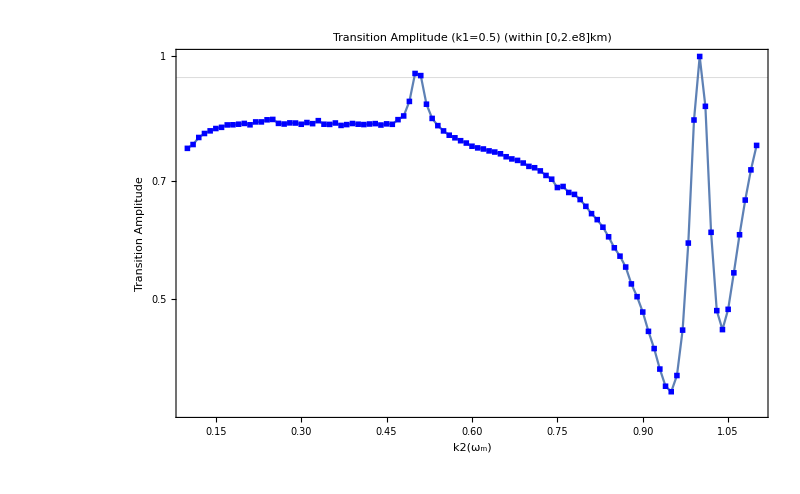

```mathematica
k2MaxAmpListDataListLogPlot=ListLogPlot[MapThread[{#1,#2}&,{k2MaxAmpListDatax,k2MaxAmpListData}],Joined->True,PlotMarkers->Style["■", Small, Blue],Frame->True,ImageSize->imgsize,PlotLabel->"Transition Amplitude (k1="<>ToString[k2MaxAmpListDatak1]<>") (within [0,"<>ToString[NumberForm[ScientificForm[Chop[MeVInverse2km[endpointNRes/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]],NumberFormat->(#1<>"e"<>#3&)],2]]<>"]km)",FrameLabel->{{"Transition Amplitude",None},{"k2(ω_m)","Fluction Wavelength (km)"}},FrameTicks->{{Automatic,None},{Automatic,k1MaxAmpListDataTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImagePadding->{{Automatic,Automatic},{Automatic,60}},PlotRange->Full,GridLines->{None, {Max@probTransitListData[{k2MaxAmpListDatak1},oneaList,onephiList,thetamVRes,endpointNRes,10,0]}}]
```

Make Plots of some of the k’s

```mathematica
pltNum[{0.5},oneaList,onephiList,thetamVRes,endpointNRes,"Only 1",Blue,None,None]
```

-Graphics-

```mathematica
(*Manipulate[pltNum[{0.5,k2},{0.1,a2},twophiList,thetamVRes,endpointNRes,ToString[k2],Blue,None,None],{{k2,0.8},0.0001,1,0.0001},{{a2,0.1},0.001,0.2}]*)
```

```mathematica
(*Table[pltNum[{0.999,k2},{0.1,0.05},twophiList,thetamVRes,endpointNRes,"A1=A2=0.1; k1=0.999,"<>"k2="<>ToString[k2],Blue,None,None],{k2,0.9,1,0.1}]*)
```

```mathematica
(*Table[pltNum[{0.999,k2},twoaList,twophiList,thetamVRes,endpointNRes,ToString[k2],Blue,None,None],{k2,0.0001,1,0.2}]*)
```

Make a list plot of different ranges

```mathematica
Import["export/resonance-destruction/k2MaxAmpListData-k1-0.5-k2-0.5MSW-range12000.dat"]
```

{{0.1,0.768263},{0.11,0.776497},{0.12,0.781937},{0.13,0.802673},{0.14,0.801045},{0.15,0.810697},{0.16,0.816906},{0.17,0.819882},{0.18,0.819538},{0.19,0.824256},{0.2,0.818292},{0.21,0.821414},{0.22,0.821081},{0.23,0.824991},{0.24,0.828741},{0.25,0.83232},{0.26,0.823411},{0.27,0.814649},{0.28,0.818876},{0.29,0.827002},{0.3,0.824093},{0.31,0.825772},{0.32,0.815434},{0.33,0.8326},{0.34,0.824029},{0.35,0.823772},{0.36,0.806671},{0.37,0.82138},{0.38,0.820391},{0.39,0.821472},{0.4,0.821968},{0.41,0.822213},{0.42,0.819484},{0.43,0.813508},{0.44,0.802362},{0.45,0.825036},{0.46,0.80903},{0.47,0.821087},{0.48,0.841519},{0.49,0.864146},{0.5,0.952666},{0.51,0.94691},{0.52,0.870096},{0.53,0.837942},{0.54,0.819151},{0.55,0.80123},{0.56,0.792873},{0.57,0.79044},{0.58,0.785815},{0.59,0.781077},{0.6,0.774005},{0.61,0.768504},{0.62,0.763625},{0.63,0.763783},{0.64,0.757579},{0.65,0.752781},{0.66,0.747354},{0.67,0.74509},{0.68,0.737721},{0.69,0.729655},{0.7,0.728528},{0.71,0.72678},{0.72,0.713551},{0.73,0.70963},{0.74,0.70387},{0.75,0.686348},{0.76,0.690024},{0.77,0.670804},{0.78,0.674614},{0.79,0.662442},{0.8,0.650456},{0.81,0.630414},{0.82,0.619565},{0.83,0.614289},{0.84,0.593271},{0.85,0.574474},{0.86,0.558698},{0.87,0.541502},{0.88,0.518568},{0.89,0.503823},{0.9,0.481719},{0.91,0.449103},{0.92,0.410531},{0.93,0.408751},{0.94,0.390186},{0.95,0.375741},{0.96,0.381643},{0.97,0.457963},{0.98,0.576149},{0.99,0.834182},{1.,0.999959},{1.01,0.866863},{1.02,0.597011},{1.03,0.47862},{1.04,0.44075},{1.05,0.476573},{1.06,0.539037},{1.07,0.601223},{1.08,0.658502},{1.09,0.718183},{1.1,0.772237}}

```mathematica
、
```

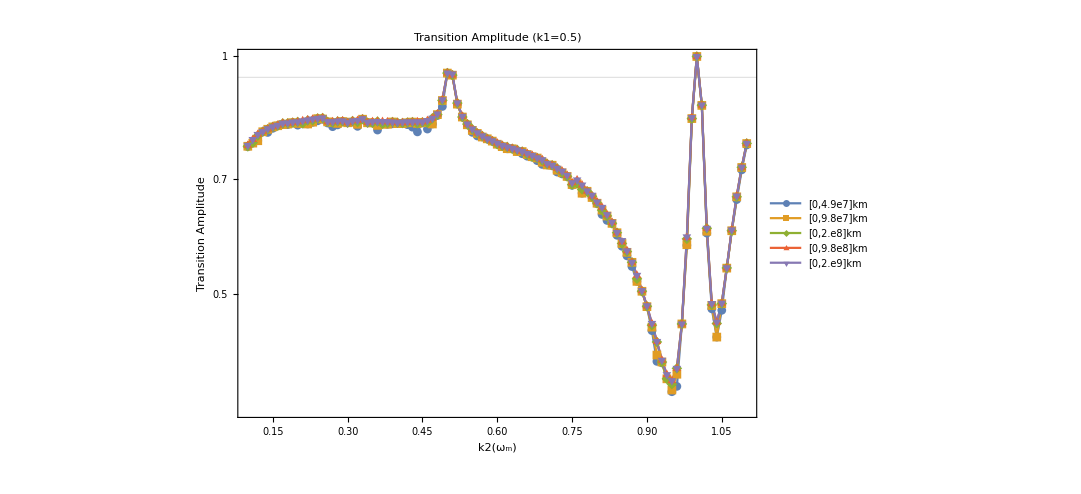

```mathematica
ListLogPlot[{
Import["export/resonance-destruction/k2MaxAmpListData-k1-0.5-k2-0.5MSW-range12000.dat"],
Import["export/resonance-destruction/k2MaxAmpListData-k1-0.5-k2-0.5MSW-range24000.dat"],
Import["export/resonance-destruction/k2MaxAmpListData-k1-0.5-k2-0.5MSW-range48000.dat"],
Import["export/resonance-destruction/k2MaxAmpListData-k1-0.5-k2-0.5MSW-range240000.dat"],
Import["export/resonance-destruction/k2MaxAmpListData-k1-0.5-k2-0.5MSW-range480000.dat"]
},Joined->True,PlotMarkers->Automatic(*{Style["■", Small, Blue],Style["", Small, Red],Style["■", Small, Orange],Style["■", Small, Black],Style["■", Small, Brown]}*),Frame->True,ImageSize->imgsize,PlotLabel->"Transition Amplitude (k1="<>ToString[k2MaxAmpListDatak1]<>")",FrameLabel->{{"Transition Amplitude",None},{"k2(ω_m)","Fluction Wavelength (km)"}},FrameTicks->{{Automatic,None},{Automatic,k1MaxAmpListDataTicks}},LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{(*FontWeight->"Bold",*)FontFamily->"Arial",FontSize->18},ImagePadding->{{Automatic,Automatic},{Automatic,60}},PlotRange->Full,GridLines->{None, {Max@probTransitListData[{k2MaxAmpListDatak1},oneaList,onephiList,thetamVRes,endpointNRes,10,0]}},PlotLegends->Placed[{
"[0,"<>ToString[NumberForm[ScientificForm[Chop[MeVInverse2km[12000/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]],NumberFormat->(#1<>"e"<>#3&)],2]]<>"]km",
"[0,"<>ToString[NumberForm[ScientificForm[Chop[MeVInverse2km[24000/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]],NumberFormat->(#1<>"e"<>#3&)],2]]<>"]km",
"[0,"<>ToString[NumberForm[ScientificForm[Chop[MeVInverse2km[48000/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]],NumberFormat->(#1<>"e"<>#3&)],2]]<>"]km",
"[0,"<>ToString[NumberForm[ScientificForm[Chop[MeVInverse2km[240000/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]],NumberFormat->(#1<>"e"<>#3&)],2]]<>"]km",
"[0,"<>ToString[NumberForm[ScientificForm[Chop[MeVInverse2km[480000/OmegaMatter[thetamVRes,thetaVRes,omegaVRes]]],NumberFormat->(#1<>"e"<>#3&)],2]]<>"]km"
},{Center,Bottom}]
]
```

## Calculate the n list that is responsible

Dip arround 1.0

Questions:
1. Why is there a dip arround 1.0?

```mathematica
Grid@Table[Part[qValueOrderdList[listNGenerator[2,6],{0.5,k2},twoaList,twophiList,thetamVRes],1;;4],{k2,1,0.8,-0.05}]
```

{{-6,4},0.} | {{-4,3},0.} | {{-2,2},0.} | {{0,1},0.}
{{2,0},0.} | {{0,1},5.26858} | {{1,0},52.5228} | {{-1,0},157.569}
{{2,0},0.} | {{0,1},10.5386} | {{1,0},52.537} | {{-1,0},157.611}
{{2,0},0.} | {{0,1},15.8104} | {{1,0},52.5538} | {{-1,0},157.661}
{{-6,5},0.} | {{2,0},0.} | {{0,1},21.0845} | {{1,0},52.5738}

```mathematica
dipEffectiveNList0point8=Flatten[ Drop[Part[qValueOrderdList[listNGenerator[2,6],{0.5,0.95},twoaList,twophiList,thetamVRes],1;;4],None,{2}],1]
```

{{2,0},{0,1},{1,0},{-1,0}}

```mathematica
widthNList[dipEffectiveNList0point8[[1]],{0.5,0.95},twoaList,twophiList,thetamVRes]
dipEffectiveNList0point8[[1]].{0.5,0.95}
```

0.000880504

1.

the corresponding wavelength is

```mathematica
MeVInverse2km[2Pi/(widthNList[dipEffectiveNList0point8[[1]],{0.5,0.95},twoaList,twophiList,thetamVRes]*OmegaMatter[thetamVRes,thetaVRes,omegaVRes])]
```

2.91455×10^7

```mathematica
(*pltNList[{dipEffectiveNList0point8[[1]]},{0.5,0.95},twoaList,twophiList,thetamVRes,endpointNRes,"List"<>ToString[dipEffectiveNList0point8[[1]]],Blue,None,None]*)
```

```mathematica
(*pltNList[{dipEffectiveNList0point8[[2]]},{0.5,0.95},twoaList,twophiList,thetamVRes,endpointNRes,"List"<>ToString[dipEffectiveNList0point8[[2]]],Blue,None,None]*)
```

```mathematica
(*pltNList[{dipEffectiveNList0point8[[3]]},{0.5,0.95},twoaList,twophiList,thetamVRes,endpointNRes,"List"<>ToString[dipEffectiveNList0point8[[3]]],Blue,None,None]*)
```